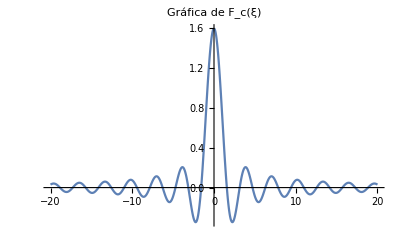

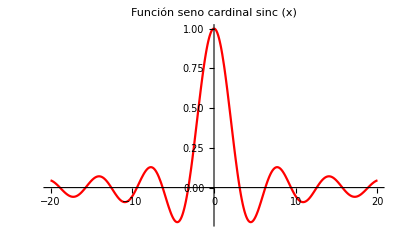

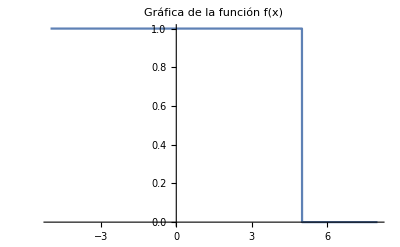

```mathematica
Plot[√(2/Pi)*Sin[2 x]/x,{x,-20,20},PlotLabel->Style["Gráfica de F_c(ξ)", FontSize->16, Black],PlotRange->All]    
Plot[Sin[x]/x,{x,-20,20}, PlotLabel->Style["Función seno cardinal sinc (x)", FontSize->16, Black],PlotRange->All, PlotStyle->{Red}]
Plot[Piecewise[{{1, x < 5},{0, x>5}}],{x,-5,8}, PlotLabel->Style["Gráfica de la función f(x)", FontSize->16,Black]]
```

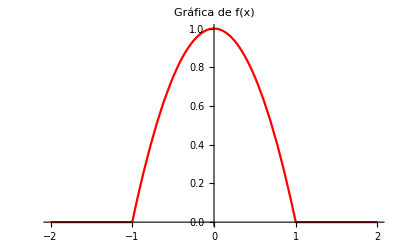

```mathematica
Plot[Piecewise[{{1-x^2,Abs[x] ≤1},{0,Abs[x]>1}}],{x,-2,2}, PlotLabel->Style["Gráfica de f(x)",FontSize->16, Black],  PlotStyle->{Red},PlotRange->All]
```

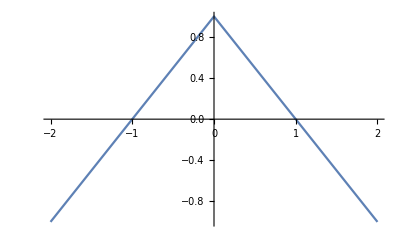

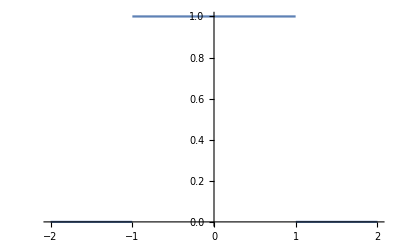

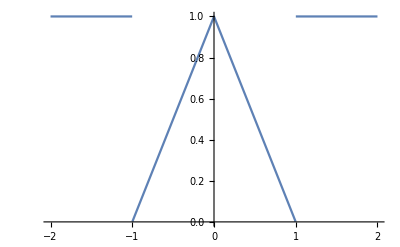

-Graphics-

```mathematica
(*Example 1.6 *)
Plot[1-Abs[x],{x,-2,2}]
Plot[HeavisideTheta[1-Abs[x]],{x,-2,2}]
Plot[1-Abs[x]*HeavisideTheta[1-Abs[x]],{x,-2,2}]
Plot[1-Abs[x],{x,-2,2}]
```